# Analytic Form of gravity disp relation

```mathematica
Subscript[γ̄, 1]^2 (1+√(1+(4  Subscript[c, 2]^2((Subscript[k, x]^2+Subscript[k, y]^2)Subscript[c, 2]^2+ Subscript[γ̄, 2]^2))/g^2))-  Subscript[γ̄, 2]^2 (1-√(1+(4 Subscript[c, 1]^2 ((Subscript[k, x]^2+Subscript[k, y]^2)Subscript[c, 1]^2+ Subscript[γ̄, 1]^2))/g^2))=0
```

Setting equal densities and no ky

```mathematica
Subscript[γ̄, 1]^2 (1+√(1+(4  c^2(Subscript[k, x]^2 c^2+ Subscript[γ̄, 2]^2))/g^2))- Subscript[γ̄, 2]^2 (1-√(1+(4 c^2 (Subscript[k, x]^2 c^2+ Subscript[γ̄, 1]^2))/g^2))=0
```

```mathematica
Subscript[γ̄, 1]^2 (g+√(g^2+4  c^2(Subscript[k, x]^2 c^2+ Subscript[γ̄, 2]^2)))- Subscript[γ̄, 2]^2 (g-√(g^2+4 c^2 (Subscript[k, x]^2 c^2+ Subscript[γ̄, 1]^2)))=0
```

```mathematica
(γ+ⅈ U1 Subscript[k, x])^2 (g+√(g^2+4 c^2 (c^2 Subscript[k, x]^2+(γ-ⅈ U1 Subscript[k, x])^2)))-(γ-ⅈ U1 Subscript[k, x])^2 (g-√(g^2+4 c^2 (c^2 Subscript[k, x]^2+(γ+ⅈ U1 Subscript[k, x])^2)))==0
```

```mathematica
(γ+ⅈ )^2 (g/(U^2 k)+√(g^2/(U^4 Subscript[k, x]^2)+4 1/M^2(1/M^2+(γ-ⅈ )^2)))-(γ-ⅈ )^2 (g/(U1^2 Subscript[k, x])-√(g^2/(U1^4 Subscript[k, x]^2)+4 1/M^2 (1/M^2 +(γ+ⅈ )^2)))==0
```

```mathematica
(γ+ⅈ )^2 (1/Fr^2+√(1/Fr^4+4 1/M^2(1/M^2+(γ-ⅈ )^2)))-(γ-ⅈ )^2 (1/Fr^2-√(1/Fr^4+4 1/M^2 (1/M^2 +(γ+ⅈ )^2)))==0
```

Where Fr= U Sqrt(kx/g) and γ = γ / (U kx)

```mathematica
Solve[(γ+ⅈ )^2 (1/Fr^2+√(1/Fr^4+4 1/M^2(1/M^2+(γ-ⅈ )^2)))-(γ-ⅈ )^2 (1/Fr^2-√(1/Fr^4+4 1/M^2 (1/M^2 +(γ+ⅈ )^2)))==0,γ]//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{γ→-√(-1-1/M^2+(ⅈ-(√(-4 ⅈ Fr^2 M^2-M^4+4 Fr^4 (1+4 M^2)))/M^2)/(2 Fr^2))},{γ→(√(-(-ⅈ M^2+2 Fr^2 (1+M^2)+√(-4 ⅈ Fr^2 M^2-M^4+4 Fr^4 (1+4 M^2)))/(Fr^2 M^2)))/(√2)},{γ→-(√((ⅈ M^2-2 Fr^2 (1+M^2)+√(-4 ⅈ Fr^2 M^2-M^4+4 Fr^4 (1+4 M^2)))/(Fr^2 M^2)))/(√2)},{γ→(√((ⅈ M^2-2 Fr^2 (1+M^2)+√(-4 ⅈ Fr^2 M^2-M^4+4 Fr^4 (1+4 M^2)))/(Fr^2 M^2)))/(√2)},{γ→-√(-1-1/M^2-(ⅈ+(√(4 ⅈ Fr^2 M^2-M^4+4 Fr^4 (1+4 M^2)))/M^2)/(2 Fr^2))},{γ→(√(-(ⅈ M^2+2 Fr^2 (1+M^2)+√(4 ⅈ Fr^2 M^2-M^4+4 Fr^4 (1+4 M^2)))/(Fr^2 M^2)))/(√2)},{γ→-(√((-ⅈ M^2-2 Fr^2 (1+M^2)+√(4 ⅈ Fr^2 M^2-M^4+4 Fr^4 (1+4 M^2)))/(Fr^2 M^2)))/(√2)},{γ→(√((-ⅈ M^2-2 Fr^2 (1+M^2)+√(4 ⅈ Fr^2 M^2-M^4+4 Fr^4 (1+4 M^2)))/(Fr^2 M^2)))/(√2)}}

```mathematica
√((ⅈ M^2-2 Fr^2 (1+M^2)+√(-4 ⅈ Fr^2 M^2-M^4+4 Fr^4 (1+4 M^2)))/(2 Fr^2 M^2))
```

```mathematica
√((ⅈ M^2-2 Fr^2 (1+M^2)+2 √(- ⅈ Fr^2 M^2-M^4/4+ Fr^4 (1+4 M^2)))/(2 Fr^2 M^2))
```

```mathematica
√(ⅈ M^2/(2 Fr^2 M^2)-(2 Fr^2 (1+M^2))/(2 Fr^2 M^2)+2/(2 Fr^2 M^2)√(- ⅈ Fr^2 M^2-M^4/4+ Fr^4 (1+4 M^2)))
```

```mathematica
√(ⅈ 1/(2 Fr^2)-(1+M^2)/M^2+1/(Fr^2 M^2)√(- ⅈ Fr^2 M^2-M^4/4+ Fr^4 (1+4 M^2)))
```

```mathematica
√(ⅈ 1/(2 Fr^2)-(1+M^2)/M^2+1/(Fr^2 M^2)Fr^2 √(- ⅈ (Fr^2 M^2)/Fr^4-M^4/(4 Fr^4)+ (1+4 M^2)))
```

```mathematica
√(ⅈ 1/(2 Fr^2)-(1+M^2)/M^2+1/M^2 √(- ⅈ M^2/Fr^2-M^4/(4 Fr^4)+ (1+4 M^2)))
```

```mathematica
√(ⅈ 1/(2 Fr^2)-(1+M^2)/M^2+1/M^2 √(- ⅈ M^2/Fr^2-M^4/(4 Fr^4)+ 1+4 M^2))
```

```mathematica
√(ⅈ 1/(2 Fr^2)-1-1/M^2+2/M √(- ⅈ 1/(4 Fr^2)-M^2/(16 Fr^4)+ 1/(4 M^2)+1))
```

```mathematica
√(ⅈ 1/(2 Fr^2)-1-1/M^2+2/M √(- ⅈ 1/(4 Fr^2)-M^2/(16 Fr^4)+ 1/(4 M^2)+1))
```

```mathematica
√(ⅈ 1/(2 Fr^2)-1-1/M^2+2/M √(1 + 1/(4 M^2)-M^2/(16 Fr^4)- ⅈ 1/(4 Fr^2)))
```

```mathematica
ReplaceAll[√(ⅈ 1/(2 Fr^2)-1-1/M^2+2/M √(1 + 1/(4 M^2)-M^2/(16 Fr^4)- ⅈ 1/(4 Fr^2))),{M->U/c,Fr->(U √(kx))/(√(g))}]
```

√(-1-c^2/U^2+(ⅈ g)/(2 kx U^2)+(2 c √(1+c^2/(4 U^2)-g^2/(16 c^2 kx^2 U^2)-(ⅈ g)/(4 kx U^2)))/U)

```mathematica
Manipulate[ReImPlot[Abs[U] kx √(-1-c^2/U^2+(ⅈ g)/(2 kx U^2)+(2 c √(1+c^2/(4 U^2)-g^2/(16 c^2 kx^2 U^2)-(ⅈ g)/(4 kx U^2)))/Abs[U]),{U,-100,100},PlotRange->{{0,100},{0,50}}],{g,0.1,10},{c,25,50},{kx,1,100000}]
```

```mathematica
Asymptotic[U kx √(-1-c^2/U^2+(ⅈ g)/(2 kx U^2)+(2 c √(1+c^2/(4 U^2)-g^2/(16 c^2 kx^2 U^2)-(ⅈ g)/(4 kx U^2)))/U),{U,∞,2}]
```

-ⅈ c kx+(ⅈ g^2+4 c^2 g kx-4 ⅈ c^4 kx^2)/(32 c kx U^2)+g/(4 U)+ⅈ kx U

The above is for when the top fluid is flowing in the positive x direction and the bottom fluid is flowing in the negative x direction.

```mathematica
Manipulate[ReImPlot[Abs[U] kx √(-1-c^2/U^2-(ⅈ g)/(2 kx U^2)+(2 c √(1+c^2/(4 U^2)-g^2/(16 c^2 kx^2 U^2)+(ⅈ g)/(4 kx U^2)))/Abs[U]),{U,-100,100}],{g,0.1,10},{c,25,50},{kx,1,1}]
```

```mathematica
Asymptotic[-U kx √(-1-c^2/U^2-(ⅈ g)/(2 kx U^2)+(2 c √(1+c^2/(4 U^2)-g^2/(16 c^2 kx^2 U^2)+(ⅈ g)/(4 kx U^2)))/-U),{U,∞,2}]
```

-ⅈ c kx-(-ⅈ g^2+4 c^2 g kx+4 ⅈ c^4 kx^2)/(32 c kx U^2)+g/(4 U)-ⅈ kx U

Above is for flows where the top fluid is going to the negative x direction and the bottom fluid is going to the positive x direction

## Disp Relation without equal and opposite fluid velocities

```mathematica
Subscript[γ̄, 1]^2 (1+√(1+(4  Subscript[c, 2]^2((Subscript[k, x]^2+Subscript[k, y]^2)Subscript[c, 2]^2+ Subscript[γ̄, 2]^2))/g^2))-  Subscript[γ̄, 2]^2 (1-√(1+(4 Subscript[c, 1]^2 ((Subscript[k, x]^2+Subscript[k, y]^2)Subscript[c, 1]^2+ Subscript[γ̄, 1]^2))/g^2))=0
```

Setting equal densities and no ky

```mathematica
Subscript[γ̄, 1]^2 (1+√(1+(4  c^2(Subscript[k, x]^2 c^2+ Subscript[γ̄, 2]^2))/g^2))- Subscript[γ̄, 2]^2 (1-√(1+(4 c^2 (Subscript[k, x]^2 c^2+ Subscript[γ̄, 1]^2))/g^2))=0
```

```mathematica
Subscript[γ̄, 1]^2 (g+√(g^2+4  c^2(Subscript[k, x]^2 c^2+ Subscript[γ̄, 2]^2)))- Subscript[γ̄, 2]^2 (g-√(g^2+4 c^2 (Subscript[k, x]^2 c^2+ Subscript[γ̄, 1]^2)))==0
```

```mathematica
ReplaceAll[ Subscript[γ̄, 1]^2 (g+√(g^2+4  c^2(Subscript[k, x]^2 c^2+ Subscript[γ̄, 2]^2)))- Subscript[γ̄, 2]^2 (g-√(g^2+4 c^2 (Subscript[k, x]^2 c^2+ Subscript[γ̄, 1]^2)))==0,{Subscript[γ̄, 2]->(γ+I*Subscript[k, x]*U2),Subscript[γ̄, 1]->(γ+I*Subscript[k, x]*U1)}]
```

-(γ+ⅈ U2 k_x)^2 (g-√(g^2+4 c^2 (c^2 k_x^2+(γ+ⅈ U1 k_x)^2)))+(γ+ⅈ U1 k_x)^2 (g+√(g^2+4 c^2 (c^2 k_x^2+(γ+ⅈ U2 k_x)^2)))==0

```mathematica
Solve[-(γ+ⅈ U2 Subscript[k, x])^2 (g-√(g^2+4 c^2 (c^2 Subscript[k, x]^2+(γ+ⅈ U1 Subscript[k, x])^2)))+(γ+ⅈ U1 Subscript[k, x])^2 (g+√(g^2+4 c^2 (c^2 Subscript[k, x]^2+(γ+ⅈ U2 Subscript[k, x])^2)))==0,γ]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{γ→1/2 ⅈ (-U1 k_x-U2 k_x-√((U1 k_x+U2 k_x)^2+2 (-ⅈ g k_x+2 c^2 k_x^2-2 U1 U2 k_x^2+k_x √(-g^2-4 ⅈ c^2 g k_x+4 c^4 k_x^2+4 c^2 U1^2 k_x^2-8 c^2 U1 U2 k_x^2+4 c^2 U2^2 k_x^2))))},{γ→1/2 ⅈ (-U1 k_x-U2 k_x+√((U1 k_x+U2 k_x)^2+2 (-ⅈ g k_x+2 c^2 k_x^2-2 U1 U2 k_x^2+k_x √(-g^2-4 ⅈ c^2 g k_x+4 c^4 k_x^2+4 c^2 U1^2 k_x^2-8 c^2 U1 U2 k_x^2+4 c^2 U2^2 k_x^2))))},{γ→1/2 ⅈ (-U1 k_x-U2 k_x-√((U1 k_x+U2 k_x)^2-2 (ⅈ g k_x-2 c^2 k_x^2+2 U1 U2 k_x^2+k_x √(-g^2-4 ⅈ c^2 g k_x+4 c^4 k_x^2+4 c^2 U1^2 k_x^2-8 c^2 U1 U2 k_x^2+4 c^2 U2^2 k_x^2))))},{γ→1/2 ⅈ (-U1 k_x-U2 k_x+√((U1 k_x+U2 k_x)^2-2 (ⅈ g k_x-2 c^2 k_x^2+2 U1 U2 k_x^2+k_x √(-g^2-4 ⅈ c^2 g k_x+4 c^4 k_x^2+4 c^2 U1^2 k_x^2-8 c^2 U1 U2 k_x^2+4 c^2 U2^2 k_x^2))))},{γ→1/2 ⅈ (-U1 k_x-U2 k_x-√((U1 k_x+U2 k_x)^2+2 ⅈ (g k_x-2 ⅈ c^2 k_x^2+2 ⅈ U1 U2 k_x^2-√(g^2 k_x^2-4 ⅈ c^2 g k_x^3-4 c^4 k_x^4-4 c^2 U1^2 k_x^4+8 c^2 U1 U2 k_x^4-4 c^2 U2^2 k_x^4))))},{γ→1/2 ⅈ (-U1 k_x-U2 k_x+√((U1 k_x+U2 k_x)^2+2 ⅈ (g k_x-2 ⅈ c^2 k_x^2+2 ⅈ U1 U2 k_x^2-√(g^2 k_x^2-4 ⅈ c^2 g k_x^3-4 c^4 k_x^4-4 c^2 U1^2 k_x^4+8 c^2 U1 U2 k_x^4-4 c^2 U2^2 k_x^4))))},{γ→1/2 ⅈ (-U1 k_x-U2 k_x-√((U1 k_x+U2 k_x)^2+2 ⅈ (g k_x-2 ⅈ c^2 k_x^2+2 ⅈ U1 U2 k_x^2+√(g^2 k_x^2-4 ⅈ c^2 g k_x^3-4 c^4 k_x^4-4 c^2 U1^2 k_x^4+8 c^2 U1 U2 k_x^4-4 c^2 U2^2 k_x^4))))},{γ→1/2 ⅈ (-U1 k_x-U2 k_x+√((U1 k_x+U2 k_x)^2+2 ⅈ (g k_x-2 ⅈ c^2 k_x^2+2 ⅈ U1 U2 k_x^2+√(g^2 k_x^2-4 ⅈ c^2 g k_x^3-4 c^4 k_x^4-4 c^2 U1^2 k_x^4+8 c^2 U1 U2 k_x^4-4 c^2 U2^2 k_x^4))))}}

### Solution 1

First check if solution is one we are looking for

```mathematica
Manipulate[ReImPlot[ ReplaceAll[1/2 ⅈ (-U1 Subscript[k, x]-U2 Subscript[k, x]-√((U1 Subscript[k, x]+U2 Subscript[k, x])^2-2 (ⅈ g Subscript[k, x]-2 c^2 Subscript[k, x]^2+2 U1 U2 Subscript[k, x]^2+Subscript[k, x] √(-g^2-4 ⅈ c^2 g Subscript[k, x]+4 c^4 Subscript[k, x]^2+4 c^2 U1^2 Subscript[k, x]^2-8 c^2 U1 U2 Subscript[k, x]^2+4 c^2 U2^2 Subscript[k, x]^2)))),{Subscript[k, x]->kx}],{U2,-300,0},PlotRange->{{-300,0},{-30,30}},PlotPoints->5000],{g,0.1,10},{c,25,50},{kx,1,100000},{U1,10,25}]
```

```mathematica
ReplaceAll[1/2 ⅈ (-U1 Subscript[k, x]-U2 Subscript[k, x]-√((U1 Subscript[k, x]+U2 Subscript[k, x])^2-2 (ⅈ g Subscript[k, x]-2 c^2 Subscript[k, x]^2+2 U1 U2 Subscript[k, x]^2+Subscript[k, x] √(-g^2-4 ⅈ c^2 g Subscript[k, x]+4 c^4 Subscript[k, x]^2+4 c^2 U1^2 Subscript[k, x]^2-8 c^2 U1 U2 Subscript[k, x]^2+4 c^2 U2^2 Subscript[k, x]^2)))),{Subscript[k, x]->kx}]//Simplify
```

-1/2 ⅈ (kx (U1+U2)+√(kx (-2 ⅈ g+4 c^2 kx+kx U1^2-2 √(-g^2-4 ⅈ c^2 g kx+4 c^2 kx^2 (c^2+(U1-U2)^2))-2 kx U1 U2+kx U2^2)))

```mathematica
-1/2 ⅈ (kx (U1+U2)+√(kx (-2 ⅈ g+4 c^2 kx+kx (U1-U2)^2-2 √(-g^2-4 ⅈ c^2 g kx+4 c^2 kx^2 (c^2+(U1-U2)^2)))))
```

```mathematica
-1/2 ⅈ (kx (U1+U2)+√(kx (-2 ⅈ g+4 c^2 kx+4 c^2 kx Mc^2-2 √(-g^2-4 ⅈ g c^2  kx+4 c^4 kx^2+16 c^4 kx^2 Mc^2))))
```

```mathematica
-1/2 ⅈ (kx (U1+U2)+√(kx (-2 ⅈ g+4 c^2 kx+4 c^2 kx Mc^2-2 √(4 c^4 kx^2(-g^2/(4 c^4 kx^2)-(ⅈ g)/(c^2 kx)+1+4 Mc^2)))))
```

```mathematica
-1/2 ⅈ (kx (U1+U2)+√(kx (-2 ⅈ g+4 c^2 kx+4 c^2 kx Mc^2- 4 c^2 kx √(-1/(4 L^2)-ⅈ/L+1+4 Mc^2))))
```

```mathematica
-1/2 ⅈ (kx (U1+U2)+√(4 c^2 kx^2 ((-2 ⅈ g)/(4 c^2 kx)+1+Mc^2- √((1-I/(2L))^2+4 Mc^2))))
```

```mathematica
-1/2 ⅈ (kx (U1+U2)+2 c kx √((- ⅈ)/(2 L)+1+Mc^2- √((1-I/(2L))^2+4 Mc^2)))
```

```mathematica
-ⅈ  c kx ((U1+U2)/(2c)+√((1-ⅈ/(2 L))+Mc^2- √((1-I/(2L))^2+4 Mc^2)))
```

```mathematica
-ⅈ  c kx ((M1+M2)/2+√((1-ⅈ/(2 L))+Mc^2- √((1-I/(2L))^2+4 Mc^2)))
```

```mathematica
γ/(c kx)== -ⅈ  (M1+Mc)-I √((1-ⅈ/(2 L))+Mc^2- √((1-I/(2L))^2+4 Mc^2))
```

Now we replot the normalized version

```mathematica
Manipulate[ReImPlot[  -ⅈ  (M1+Mc)-I √((1-ⅈ/(2 L))+Mc^2- √((1-I/(2L))^2+4 Mc^2)),{Mc,-10,0},PlotRange->{{-10,0},{-1,2}},PlotPoints->5000],{L,1,1000},{M1,0,10},{M2,4,25}]
```

```mathematica
Series[  -ⅈ  ((M1+M2)/2+√((1-ⅈ/(2 L))+Mc^2- √((1-I/(2L))^2+4 Mc^2))),{Mc,∞,1}]//Simplify
```

-ⅈ Mc-1/2 ⅈ (-2+M1+M2)-1/(4 L Mc)+O[1/Mc]^2

### Solution 2 - Root we are looking for with Negative real part

Test out next solution

```mathematica
Manipulate[ReImPlot[ ReplaceAll[1/2 ⅈ (-U1 Subscript[k, x]-U2 Subscript[k, x]+√((U1 Subscript[k, x]+U2 Subscript[k, x])^2+2 ⅈ (g Subscript[k, x]-2 ⅈ c^2 Subscript[k, x]^2+2 ⅈ U1 U2 Subscript[k, x]^2-√(g^2 Subscript[k, x]^2-4 ⅈ c^2 g Subscript[k, x]^3-4 c^4 Subscript[k, x]^4-4 c^2 U1^2 Subscript[k, x]^4+8 c^2 U1 U2 Subscript[k, x]^4-4 c^2 U2^2 Subscript[k, x]^4)))),{Subscript[k, x]->kx}],{U2,10,300},PlotRange->{{0,300},{-55,15}},PlotPoints->5000],{g,0.1,10},{c,25,50},{kx,1,100000},{U1,10,25}]
```

```mathematica
ReplaceAll[1/2 ⅈ (-U1 Subscript[k, x]-U2 Subscript[k, x]+√((U1 Subscript[k, x]+U2 Subscript[k, x])^2+2 ⅈ (g Subscript[k, x]-2 ⅈ c^2 Subscript[k, x]^2+2 ⅈ U1 U2 Subscript[k, x]^2-√(g^2 Subscript[k, x]^2-4 ⅈ c^2 g Subscript[k, x]^3-4 c^4 Subscript[k, x]^4-4 c^2 U1^2 Subscript[k, x]^4+8 c^2 U1 U2 Subscript[k, x]^4-4 c^2 U2^2 Subscript[k, x]^4)))),{Subscript[k, x]->kx}]//Simplify
```

1/2 ⅈ (-kx (U1+U2)+√(2 ⅈ g kx+4 c^2 kx^2+kx^2 U1^2-2 ⅈ √(kx^2 (g^2-4 ⅈ c^2 g kx-4 c^2 kx^2 (c^2+(U1-U2)^2)))-2 kx^2 U1 U2+kx^2 U2^2))

```mathematica
1/2 ⅈ (-kx (U1+U2)+√(2 ⅈ g kx+4 c^2 kx^2+kx^2 U1^2-2 kx^2 U1 U2+kx^2 U2^2-2 ⅈ √(kx^2 (g^2-4 ⅈ c^2 g kx-4 c^2 kx^2 (c^2+(U1-U2)^2)))))
```

```mathematica
1/2 ⅈ (-kx (U1+U2)+√(2 ⅈ g kx+4 c^2 kx^2+4 c^2 kx^2 Mc^2-2 ⅈ √(kx^2 (g^2-4 ⅈ c^2 g kx-4 c^4 kx^2 (1+4 Mc^2)))))
```

```mathematica
1/2 ⅈ (-kx (U1+U2)+√(2 ⅈ g kx+4 c^2 kx^2+4 c^2 kx^2 Mc^2-2 ⅈ √(4 c^4 kx^4 (g^2/(4 c^4 kx^2)-(4 ⅈ c^2 g kx)/(4 c^4 kx^2)-(1+4 Mc^2)))))
```

```mathematica
1/2 ⅈ (-kx (U1+U2)+√(2 ⅈ g kx+4 c^2 kx^2+4 c^2 kx^2 Mc^2- ⅈ 4 c^2 kx^2 √(1/(4 L^2)-ⅈ/L-1-4 Mc^2)))
```

```mathematica
1/2 ⅈ (-kx (U1+U2)+√(2 ⅈ g kx+4 c^2 kx^2+4 c^2 kx^2 Mc^2- ⅈ 4 c^2 kx^2 √(-(1+ⅈ/(2L))^2-4 Mc^2)))
```

```mathematica
1/2 ⅈ (-kx (U1+U2)+2c kx √((ⅈ g)/(2 c^2 kx)+1+Mc^2- ⅈ √(-(1+ⅈ/(2L))^2-4 Mc^2)))
```

```mathematica
1/2 ⅈ (-kx (U1+U2)+2c kx √(ⅈ/(2 L)+1+Mc^2-  √((1+ⅈ/(2L))^2+4 Mc^2)))
```

```mathematica
ⅈ c kx(- (U1+U2)/(2 c)+√((1+ⅈ/(2 L))+Mc^2-  √((1+ⅈ/(2L))^2+4 Mc^2)))
```

```mathematica
ⅈ c kx(- (M1+M2)/2+√((1+ⅈ/(2 L))+Mc^2-  √((1+ⅈ/(2L))^2+4 Mc^2)))
```

Now we plot

```mathematica
Manipulate[ReImPlot[ ⅈ (- (M1+Mc)+√((1+ⅈ/(2 L))+Mc^2-  √((1+ⅈ/(2L))^2+4 Mc^2))),{Mc,0,30},PlotRange->{{0,3},{-2,1}},PlotPoints->5000],{L,1,1000},{M1,0,10},{M2,4,25}]
```

```mathematica
Series[ⅈ (- (M1+M2)/2+√((1+ⅈ/(2 L))+Mc^2-  √((1+ⅈ/(2L))^2+4 Mc^2))),{Mc,∞,1}]//Simplify
```

ⅈ Mc-1/2 ⅈ (2+M1+M2)-1/(4 L Mc)+O[1/Mc]^2

### Solution 3 - Root when Mc < 0

Now we try the next solution

```mathematica
Manipulate[ReImPlot[ ReplaceAll[1/2 ⅈ (-U1 Subscript[k, x]-U2 Subscript[k, x]-√((U1 Subscript[k, x]+U2 Subscript[k, x])^2+2 ⅈ (g Subscript[k, x]-2 ⅈ c^2 Subscript[k, x]^2+2 ⅈ U1 U2 Subscript[k, x]^2-√(g^2 Subscript[k, x]^2-4 ⅈ c^2 g Subscript[k, x]^3-4 c^4 Subscript[k, x]^4-4 c^2 U1^2 Subscript[k, x]^4+8 c^2 U1 U2 Subscript[k, x]^4-4 c^2 U2^2 Subscript[k, x]^4)))),{Subscript[k, x]->kx}],{U2,-300,300},PlotRange->{{-300,300},{0,65}},PlotPoints->5000],{g,0.1,10},{c,25,50},{kx,1,100000},{U1,10,25}]
```

```mathematica
ReplaceAll[1/2 ⅈ (-U1 Subscript[k, x]-U2 Subscript[k, x]-√((U1 Subscript[k, x]+U2 Subscript[k, x])^2+2 ⅈ (g Subscript[k, x]-2 ⅈ c^2 Subscript[k, x]^2+2 ⅈ U1 U2 Subscript[k, x]^2-√(g^2 Subscript[k, x]^2-4 ⅈ c^2 g Subscript[k, x]^3-4 c^4 Subscript[k, x]^4-4 c^2 U1^2 Subscript[k, x]^4+8 c^2 U1 U2 Subscript[k, x]^4-4 c^2 U2^2 Subscript[k, x]^4)))),{Subscript[k, x]->kx}]//Simplify
```

-1/2 ⅈ (kx (U1+U2)+√(2 ⅈ g kx+4 c^2 kx^2+kx^2 U1^2-2 ⅈ √(kx^2 (g^2-4 ⅈ c^2 g kx-4 c^2 kx^2 (c^2+(U1-U2)^2)))-2 kx^2 U1 U2+kx^2 U2^2))

```mathematica
-1/2 ⅈ (kx (U1+U2)+√(2 ⅈ g kx+4 c^2 kx^2+kx^2 U1^2-2 kx^2 U1 U2+kx^2 U2^2-2 ⅈ √(4 c^4 kx^4 (1/(4 L)-ⅈ/L- (1+4 Mc^2)))))
```

```mathematica
-1/2 ⅈ (kx (U1+U2)+√(2 ⅈ g kx+4 c^2 kx^2+kx^2 U1^2-2 kx^2 U1 U2+kx^2 U2^2- 4 c^2 kx^2 √(( 1+ⅈ/(2 L))^2+4 Mc^2)))
```

```mathematica
-1/2 ⅈ (kx (U1+U2)+ 2 c kx √((ⅈ g)/(2 c^2 kx)+1+Mc^2- √(( 1+ⅈ/(2 L))^2+4 Mc^2)))
```

```mathematica
- ⅈ  c kx( (M1+M2)/2+√((1+ⅈ/(2 L))+Mc^2- √(( 1+ⅈ/(2 L))^2+4 Mc^2)))
```

```mathematica
- ⅈ  c kx( (M1+Mc)+√((1+ⅈ/(2 L))+Mc^2- √(( 1+ⅈ/(2 L))^2+4 Mc^2)))
```

```mathematica
γ/(c kx)==- ⅈ  (M1+Mc)-i √((1+ⅈ/(2 L))+Mc^2- √(( 1+ⅈ/(2 L))^2+4 Mc^2))
```

```mathematica
Manipulate[ReImPlot[  - ⅈ  ( (M1+Mc)+√((1+ⅈ/(2 L))+Mc^2- √(( 1+ⅈ/(2 L))^2+4 Mc^2))),{Mc,-10,0},PlotRange->{{-10,0},{0,3}},PlotPoints->5000],{L,1,1000},{M1,0,10},{M2,2,25}]
```

```mathematica
Series[  - ⅈ  ( (M1+Mc)+√((1+ⅈ/(2 L))+Mc^2- √(( 1+ⅈ/(2 L))^2+4 Mc^2))),{Mc,-∞,1}]
```

-ⅈ (-1+M1)-1/(4 L Mc)+O[1/Mc]^2

### Solution 4 - Root we are looking for with positive real component

Test the last solution

```mathematica
Manipulate[ReImPlot[ ReplaceAll[1/2 ⅈ (-U1 Subscript[k, x]-U2 Subscript[k, x]+√((U1 Subscript[k, x]+U2 Subscript[k, x])^2-2 (ⅈ g Subscript[k, x]-2 c^2 Subscript[k, x]^2+2 U1 U2 Subscript[k, x]^2+Subscript[k, x] √(-g^2-4 ⅈ c^2 g Subscript[k, x]+4 c^4 Subscript[k, x]^2+4 c^2 U1^2 Subscript[k, x]^2-8 c^2 U1 U2 Subscript[k, x]^2+4 c^2 U2^2 Subscript[k, x]^2)))),{Subscript[k, x]->kx}],{U2,10,300},PlotRange->{{0,300},{-65,15}},PlotPoints->5000],{g,0.1,10},{c,25,50},{kx,1,100000},{U1,10,25}]
```

```mathematica
ReplaceAll[1/2 ⅈ (-U1 Subscript[k, x]-U2 Subscript[k, x]+√((U1 Subscript[k, x]+U2 Subscript[k, x])^2-2 (ⅈ g Subscript[k, x]-2 c^2 Subscript[k, x]^2+2 U1 U2 Subscript[k, x]^2+Subscript[k, x] √(-g^2-4 ⅈ c^2 g Subscript[k, x]+4 c^4 Subscript[k, x]^2+4 c^2 U1^2 Subscript[k, x]^2-8 c^2 U1 U2 Subscript[k, x]^2+4 c^2 U2^2 Subscript[k, x]^2)))),{Subscript[k, x]->kx}]//Simplify
```

1/2 ⅈ (-kx (U1+U2)+√(kx (-2 ⅈ g+4 c^2 kx+kx U1^2-2 √(-g^2-4 ⅈ c^2 g kx+4 c^2 kx^2 (c^2+(U1-U2)^2))-2 kx U1 U2+kx U2^2)))

```mathematica
1/2 ⅈ (-kx (U1+U2)+√(kx (-2 ⅈ g+4 c^2 kx+kx U1^2-2 kx U1 U2+kx U2^2-2 √(-g^2-4 ⅈ c^2 g kx+4 c^2 kx^2 (c^2+(U1-U2)^2)))))
```

```mathematica
1/2 ⅈ (-kx (U1+U2)+√(kx (-2 ⅈ g+4 c^2 kx+kx U1^2-2 kx U1 U2+kx U2^2-2 √(-g^2-4 ⅈ c^2 g kx+4 c^4 kx^2 (1+((U1-U2)/c)^2)))))
```

```mathematica
1/2 ⅈ (-kx (U1+U2)+√(kx (-2 ⅈ g+4 c^2 kx+kx U1^2-2 kx U1 U2+kx U2^2-2 √(4 c^4 kx^2 (-g^2/(4 c^4 kx^2)-(ⅈ  g)/(c^2 kx)+1+((U1-U2)/c)^2)))))
```

```mathematica
1/2 ⅈ (-kx (U1+U2)+√(kx (-2 ⅈ g+4 c^2 kx+kx (U1- U2)^2- 4 c^2 kx √(-g^2/(4 c^4 kx^2)-(ⅈ  g)/(c^2 kx)+1+((U1-U2)/c)^2))))
```

```mathematica
1/2 ⅈ (-kx (U1+U2)+√(4 c^2 kx^2 ((-2 ⅈ g)/(4 c^2 kx)+1+(kx (U1- U2)^2)/(4 c^2 kx)-√(-g^2/(4 c^4 kx^2)-(ⅈ  g)/(c^2 kx)+1+((U1-U2)/c)^2))))
```

```mathematica
1/2 ⅈ (-kx (U1+U2)+ 2 c kx √((- ⅈ g)/(2 c^2 kx)+1+(U1- U2)^2/(4 c^2)-√(-g^2/(4 c^4 kx^2)-(ⅈ  g)/(c^2 kx)+1+((U1-U2)/c)^2)))
```

```mathematica
ⅈ  c kx (-(U1+U2)/(2 c)+ √((- ⅈ g)/(2 c^2 kx)+1+(U1- U2)^2/(4 c^2)-√(-g^2/(4 c^4 kx^2)-(ⅈ  g)/(c^2 kx)+1+((U1-U2)/c)^2)))
```

```mathematica
ⅈ  c kx (-(U1+U2)/(2 c)+ √((- ⅈ g)/(2 c^2 kx)+1+(U1- U2)^2/(4 c^2)-√((1-(ⅈ  g)/(2 c^2 kx))^2+((U1-U2)/c)^2)))
```

```mathematica
ⅈ  c kx (-(M1+M2)/2+ √((- ⅈ)/(2 L)+1+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2)))
```

Solution is then

```mathematica
γ/(c kx)== ⅈ  (-(M1+Mc)+ √((- ⅈ)/(2 L)+1+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2)))
```

```mathematica
γ/(c kx)== -I(M1+Mc)+I √((1- ⅈ/(2 L))+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2))
```

Below is solution for positive growth-rate when Mc<0

```mathematica
γ/(c kx)==- ⅈ  (M1+Mc)-i √((1+ⅈ/(2 L))+Mc^2- √(( 1+ⅈ/(2 L))^2+4 Mc^2))
```

Below is for negative growth-rate when Mc<0

```mathematica
γ/(c kx)== -ⅈ  (M1+Mc)-I √((1-ⅈ/(2 L))+Mc^2- √((1-I/(2L))^2+4 Mc^2))
```

```mathematica
L=(c^2 k)/g
```

```mathematica
N[500^2/10]
```

25000.

```mathematica
Solve[500^2/gg==10,gg]
```

{{gg→25000}}

```mathematica
testfun[M1_,Mc_,L_]:=-ⅈ   (M1+Mc)+ I √((1- ⅈ/(2 L))+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2))
```

```mathematica
Manipulate[ReImPlot[ -ⅈ   (M1+Mc)+ I √((1- ⅈ/(2 L))+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2)),{Mc,0,2},PlotRange->{{0,2},{0,0.75}},PlotPoints->5000,ImageSize->Large],{L,400,1000},{M1,0,10}]
```

```mathematica
FindRoot[Re[testfun[0,Mc,1]]==Re[testfun[0,Mc,100000]],{Mc,0.7}]
```

{Mc→0.742011}

```mathematica
N[(√2)/2]
```

0.707107

```mathematica
FindRoot[Re[testfun[0,Mc,1]]==Re[testfun[0,Mc,10000000]],{Mc,0.7}]
```

{Mc→0.742011}

```mathematica
Manipulate[ReImPlot[ {(testfun[M1,Mc,L1]),(testfun[M1,Mc,L2])},{Mc,0,2},PlotRange->{{0,2},{0,0.75}},ImageSize->Large],{L1,1,0.1},{M1,0,10},{L2,1,10}]
```

```mathematica
Manipulate[ReImPlot[ Re[(testfun[M1,Mc,L1])-(testfun[M1,Mc,L2])],{Mc,0,2},PlotPoints->5000,ImageSize->Large],{L1,1,100000},{M1,0,10},{L2,1,100000}]
```

```mathematica
Manipulate[Plot[ { I √((1- ⅈ/(2 L))+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2))+ I √((1)+Mc^2-√(1+4 Mc^2))},{Mc,0,2},PlotRange->{{0,2},{0,0.75}},PlotPoints->5000,ImageSize->Large],{L,400,1000},{M1,0,10}]
```

```mathematica
Series[  ⅈ  c kx (-(U1+U2)/(2 c)+ √((- ⅈ g)/(2 c^2 kx)+1+(U1- U2)^2/(4 c^2)-√((1-(ⅈ  g)/(2 c^2 kx))^2+((U1-U2)/c)^2))),{U2,∞,1}]//FullSimplify
```

-(ⅈ kx (U2-c √(U2^2/c^2)) U2)/(2 U2)-(ⅈ kx (2 c U2+U1 U2+c U1 √(U2^2/c^2)))/(2 U2)+(c g √(U2^2/c^2))/(2 U2 U2)+O[1/U2]^2

```mathematica
-ⅈ kx ( c +U1 )+g/(2 U2)
```

```mathematica
Manipulate[ReImPlot[ -ⅈ   (M1+Mc)+ I √((1- ⅈ/(2 L))+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2)),{Mc,-10,10},PlotRange->{{-5,5},{-2,2}},PlotPoints->5000],{L,400,1000},{M1,0,10},{M2,2,25}]
```

```mathematica
Solve[+ I √((1- ⅈ/(2 L))+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2))==0,Mc]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{Mc→0},{Mc→-(√(ⅈ+2 L))/(√L)},{Mc→(√(ⅈ+2 L))/(√L)}}

```mathematica
Solve[+ I √((1+ ⅈ/(2 L))+Mc^2-√((1+ⅈ/(2 L))^2+4 Mc^2))==0,Mc]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{Mc→0},{Mc→-(√(-ⅈ+2 L))/(√L)},{Mc→(√(-ⅈ+2 L))/(√L)}}

```mathematica
Solve[- I √((1+ ⅈ/(2 L))+Mc^2-√((1+ⅈ/(2 L))^2+4 Mc^2))==0,Mc]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{Mc→0},{Mc→-(√(-ⅈ+2 L))/(√L)},{Mc→(√(-ⅈ+2 L))/(√L)}}

```mathematica
Manipulate[ReImPlot[   - ⅈ(M1+Mc)+ⅈ √((1+ⅈ/(2 L))+Mc^2-  √((1+ⅈ/(2L))^2+4 Mc^2)),{Mc,-10,10},PlotRange->{{-5,5},{-2,2}},PlotPoints->5000],{L,10,1000},{M1,0,10}]
```

```mathematica
Series[ⅈ   (-(M1)-Mc+ √((- ⅈ)/(2 L)+1+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2))),{Mc,∞,2}]//Simplify
```

-ⅈ (1+M1)+1/(4 L Mc)-(ⅈ (ⅈ+2 L)^2)/(32 L^2 Mc^2)+O[1/Mc]^3

```mathematica
Expand[ⅈ (ⅈ+2 L)^2]/(32 L^2 Mc^2)
```

(-ⅈ-4 L+4 ⅈ L^2)/(32 L^2 Mc^2)

```mathematica
(-4 L)/(32 L^2 Mc^2)-I(1-4  L^2)/(32 L^2 Mc^2)
```

```mathematica
-1/(8 L Mc^2)-I(1-4  L^2)/(32 L^2 Mc^2)
```

```mathematica
ReplaceAll[-1/(8 L Mc^2)-I(1-4  L^2)/(32 L^2 Mc^2),{L->(c^2 k)/g,Mc->(U2-U1)/(2c)}]
```

-g/(2 k (-U1+U2)^2)-(ⅈ g^2 (1-(4 c^4 k^2)/g^2))/(8 c^2 k^2 (-U1+U2)^2)

```mathematica
-g/(2 k (-U1+U2)^2)-(ⅈ (g^2-4 c^4 k^2))/(8 c^2 k^2 (-U1+U2)^2)
```

Remove normalization on gamma k c

```mathematica
-(g c)/(2  (-U1+U2)^2)-(ⅈ (g^2-4 c^4 k^2))/(8 c k (-U1+U2)^2)
```

Now they match

```mathematica
(ⅈ ( g^2-4 c1^4  k^2) Sec[θ]^2)/(8 c1 k)
```

```mathematica
Simplify[- ⅈ(M2-M1) -ⅈ (1+M1)-1/(4 L Mc)]
```

-ⅈ-ⅈ M2-1/(4 L Mc)

```mathematica
Series[ⅈ   (-(M1)-Mc+ √((- ⅈ)/(2 L)+1+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2))),{Mc,∞,1}]//Simplify
```

-ⅈ (1+M1)+1/(4 L Mc)+O[1/Mc]^2

```mathematica
Manipulate[LogLogPlot[ Re[ I √((1- ⅈ/(2 L))+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2))]-1/(4 L Mc),{Mc,0,100},PlotRange->{{0,100},{-2,2}},PlotPoints->5000],{L,10,1000},{M1,0,10}]
```

```mathematica
Series[ⅈ c kx((U1/(2c)+U2/(2c))+√((1- (ⅈ g)/(2 c^2 kx))+(U2-U1)^2/(4 c^2) -√((1 -ⅈ g/(2 c^2 kx) )^2+(U2-U1)^2/c^2))),{U2,∞,1}]//FullSimplify
```

(ⅈ kx (U2+c √(U2^2/c^2)) U2)/(2 U2)-(ⅈ kx (2 c U2-U1 U2+c U1 √(U2^2/c^2)))/(2 U2)+(c g √(U2^2/c^2))/(2 U2 U2)+O[1/U2]^2

```mathematica
ⅈ kx U2 -ⅈ kx c +g/(2  U2)
```

## Double Checking Limits of results

```mathematica
Manipulate[ReImPlot[I √((1- ⅈ/(2 L))+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2)),{Mc,0,√2}],{L,1,1000}]
```

```mathematica
ReplaceAll[I √((1- ⅈ/(2 L))+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2)),L->(c^2 k)/g]
```

ⅈ √(1-(ⅈ g)/(2 c^2 k)+Mc^2-√((1-(ⅈ g)/(2 c^2 k))^2+4 Mc^2))

```mathematica
Manipulate[{N[ⅈ √(1-(ⅈ g)/(2 c^2 k)+Mc^2-√((1-(ⅈ g)/(2 c^2 k))^2+4 Mc^2))],N[(ⅈ √(1-(ⅈ g)/(2 c^2 k)+Mc^2-√((1-(ⅈ g)/(2 c^2 k))^2+4 Mc^2)))^2],N[( -I √(1+Mc^2-√(1^2+4 Mc^2)))],N[( -I √(1+Mc^2-√(1^2+4 Mc^2)))^2]},{Mc,0,√2},{g,1,-1},{k,1,1},{c,1,100}]
```

```mathematica
Manipulate[{N[ √(-1*(1-(ⅈ g)/(2 c^2 k)+Mc^2-√((1-(ⅈ g)/(2 c^2 k))^2+4 Mc^2)))],N[( √(-1*(1-(ⅈ g)/(2 c^2 k)+Mc^2-√((1-(ⅈ g)/(2 c^2 k))^2+4 Mc^2))))^2],N[( -√(-1*(1+Mc^2-√(1^2+4 Mc^2))))],N[( -√(-1*(1+Mc^2-√(1^2+4 Mc^2))))^2]},{Mc,0,√2},{g,1,-1},{k,1,1},{c,1,100}]
```

```mathematica
Manipulate[N[(ⅈ √(1-(ⅈ g)/(2 c^2 k)+Mc^2-√((1-(ⅈ g)/(2 c^2 k))^2+4 Mc^2)))^2],{Mc,0,√2},{g,10,-10},{k,1,1},{c,1,100}]
```

```mathematica
Manipulate[ReImPlot[ⅈ √(1-(ⅈ g)/(2 c^2 k)+Mc^2-√((1-(ⅈ g)/(2 c^2 k))^2+4 Mc^2)),{g,1,-1}],{Mc,0,√2},{k,1,1},{c,1,100}]
```

```mathematica
I √((1- ⅈ/(2 L))+Mc^2-√((1-ⅈ/(2 L))^2+4 Mc^2))
```

```mathematica
Simplify[√(1-ⅈ/(2 L)+Mc^2-re[1-1/(4 L^2)+4 Mc^2,-1/L]),L>0]
```

√(1-ⅈ/(2 L)+Mc^2+(ⅈ √(-1+1/(4 L^2)-4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2)-(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2))

```mathematica
Simplify[I*re[1+Mc^2-(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2),-1/(2 L)+(√(-1+1/(4 L^2)-4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2)]]
```

1/(2 √2)ⅈ (2 √(1+Mc^2-(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2)+√((-1/(2 L)+(√(-1+1/(4 L^2)-4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2))^2+(1+Mc^2-(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2))^2))+2 ⅈ √(-1-Mc^2+(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2)+√((-1/(2 L)+(√(-1+1/(4 L^2)-4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2))^2+(1+Mc^2-(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2))^2)) Sign[-1/(2 L)+(√(-1+1/(4 L^2)-4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2)])

```mathematica
Manipulate[Plot[-1/(2 L)+(√(-1+1/(4 L^2)-4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2),{Mc,0.00001,10}],{L,1,1000000}]
```

```mathematica
1/(√2) (I √(1+Mc^2-(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2)+√((-1/(2 L)+(√(-1+1/(4 L^2)-4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2))^2+(1+Mc^2-(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2))^2))+ √(-1-Mc^2+(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2)+√((-1/(2 L)+(√(-1+1/(4 L^2)-4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2))^2+(1+Mc^2-(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2))^2)) )
```

```mathematica
Manipulate[LogLogPlot[√(-1-Mc^2+(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2)+√((-1/(2 L)+(√(-1+1/(4 L^2)-4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2))^2+(1+Mc^2-(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2))^2)),{L,1,1000000}],{Mc,0.00001,10}]
```

```mathematica
Manipulate[Plot[√(-1-Mc^2+(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2)+√((-1/(2 L)+(√(-1+1/(4 L^2)-4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2))^2+(1+Mc^2-(√(1-1/(4 L^2)+4 Mc^2+√(1/L^2+(1-1/(4 L^2)+4 Mc^2)^2)))/(√2))^2)),{Mc,0,√2},PlotRange->Full],{L,0.1,1000}]
```

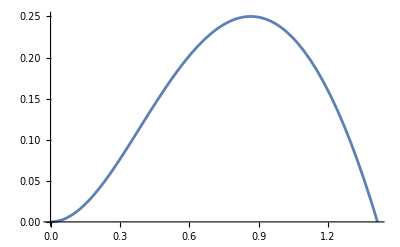

```mathematica
Plot[( -I √(1+Mc^2-√(1^2+4 Mc^2)))^2,{Mc,0,√2}]
```

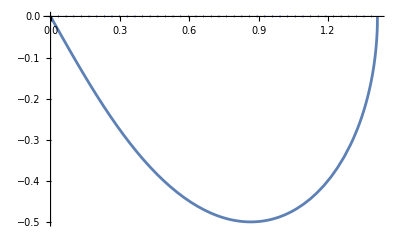

```mathematica
ReImPlot[ I √(1+Mc^2-√(1^2+4 Mc^2)),{Mc,0,√2}]
```

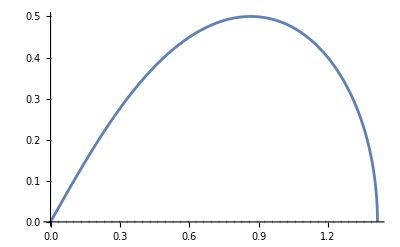

```mathematica
ReImPlot[- I √(1+Mc^2-√(1^2+4 Mc^2)),{Mc,0,√2}]
```

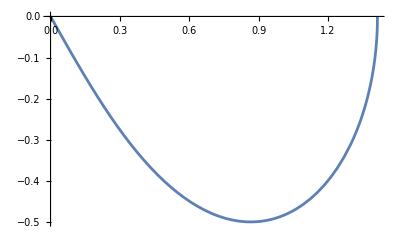

```mathematica
Plot[-√(-1(1+Mc^2-√(1^2+4 Mc^2))),{Mc,0,√2}]
```

```mathematica
N[√(1+4)]
```

2.23607

```mathematica
N[1+1-√5]
```

-0.236068

```mathematica
N[√(0.2360679774997898)]
```

0.485868

```mathematica
N[-√(0.2360679774997898)]
```

-0.485868

```mathematica
N[√(-0.2360679774997898)]
```

0.+0.485868 ⅈ

```mathematica
N[I√(-0.2360679774997898)]
```

-0.485868+0. ⅈ

```mathematica
N[-I√(-0.2360679774997898)]
```

0.485868+0. ⅈ

```mathematica
N[√(1+1-√5)]
```

0.+0.485868 ⅈ

```mathematica
N[√(4)]
```

2.

```mathematica
N[-√(4)]
```

-2.

```mathematica
N[√(-4)]
```

0.+2. ⅈ

```mathematica
N[I√(-4)]
```

-2.

```mathematica
N[-I√(-4)]
```

2.

```mathematica
Solve
```

Next should give me about 0.51 with L=1 and Mc=1

```mathematica
N[(1-I/2)^2+4]
```

4.75-1. ⅈ

```mathematica
N[√(4.75-1. ⅈ)]
```

2.19136-0.228169 ⅈ

```mathematica
re[r_,i_]:=√(1/2(√(r^2+i^2)+r))+I*Sign[i] √(1/2(√(r^2+i^2)-r))
```

```mathematica
re[4.75,-1]
```

2.19136-0.228169 ⅈ

```mathematica
N[(1-I/2)+1-(2.191360531694511-0.22816875305012704 ⅈ)]
```

-0.191361-0.271831 ⅈ

```mathematica
N[√(-0.19136053169451106-0.27183124694987293 ⅈ)]
```

0.265586-0.511758 ⅈ

```mathematica
I*(0.265585707839059-0.5117580482052871 ⅈ)
```

0.511758+0.265586 ⅈ

```mathematica
re[1+1-2.191360531694511,-1/2+0.22816875305012704]
```

0.265586-0.511758 ⅈ

```mathematica
ReplaceAll[-(γ+ⅈ U2 Subscript[k, x])^2 (g-√(g^2+4 c^2 (c^2 Subscript[k, x]^2+(γ+ⅈ U1 Subscript[k, x])^2)))+(γ+ⅈ U1 Subscript[k, x])^2 (g+√(g^2+4 c^2 (c^2 Subscript[k, x]^2+(γ+ⅈ U2 Subscript[k, x])^2))),γ->γ^(1/2)]
```

-(√γ+ⅈ U2 k_x)^2 (g-√(g^2+4 c^2 (c^2 k_x^2+(√γ+ⅈ U1 k_x)^2)))+(√γ+ⅈ U1 k_x)^2 (g+√(g^2+4 c^2 (c^2 k_x^2+(√γ+ⅈ U2 k_x)^2)))